# RF Modulation Sweep (Frequency) - Photon Correlation Counts

## Last Updated: 05/14/2022

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

## General

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[Power::infy];
Off[FindFit::nrjnum];
Off[Infinity::indet];
];
```

## Functions

### General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

### Dataset Processing

```mathematica
(*import raw counts and demodulate*)
ProcessDatasetCounts[filename_]:=Module[
{
(*actual data*)
dataset,
datasetFrequencies=Import[filename,{"/datasets/xArr"}],
datasetCounts=Import[filename,{"/datasets/results"}],
correlatedSignal,correlatedAmplitude,correlatedPhase,
(*parameters*)
modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],
(*processing*)
results
},

(*refine dataset*)
dataset=AssociationThread[datasetFrequencies->datasetCounts];
(*dataset=KeySort[dataset];*)

(*demodulate counts*)
correlatedSignal=KeyValueMap[
Total[Exp[ⅈ*(2*π*#1*1*^6)*#2]]/Length[#2]&,
dataset
];
{correlatedAmplitude,correlatedSignal}=Transpose[AbsArg[correlatedSignal]];

(*format data*)
results=Transpose[
{datasetFrequencies,ConstantArray[shimVoltage,Length[correlatedAmplitude]],##}&@@{correlatedAmplitude,correlatedSignal}
];

(*clean up mess*)
Remove[dataset,datasetFrequencies,datasetCounts];
ClearSystemCache[];
ClearInOut[];

(*return dataset*)
Return[results];
]
```

```mathematica
(*import already demodulated dataset*)
ProcessDataset[filename_]:=Module[
{
(*actual data*)
datasetRaw=Import[filename,{"/datasets/results"}],
(*parameters*)
(*modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],*)
(*processing*)
results
},

(*refine dataset*)
(*dataset=KeySort[dataset];*)

(*format data*)
(*results=Transpose[
(datasetRaw[[;;,1]],ConstantArray[shimVoltage,Length[datasetRaw]],datasetRaw[[;;,3]],datasetRaw[[;;,4]]}
];*)
results=datasetRaw;

(*clean up mess*)
Remove[datasetRaw];
ClearSystemCache[];
ClearInOut[];

(*return dataset*)
Return[results];
]
```

## User Input

## Parameters

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2023-05-17";
(*directoryString="/Volumes/groups/motion/Data/2023-04/2023-04-19";*)
(*directoryString="C:\\Users\\EGGS2\\Documents\\datatmp_rf";*)
(*directoryString="/Users/claytonho/Documents/Research/Science/Micromotion/RF Modulation";*)
```

```mathematica
(*select run*)
rid=21076;
```

```mathematica
(*data limit fitting tmp todo*)
tmpParam=10;
```

## Process User Input

```mathematica
(*select file with give RID from all subdirectories*)
filenamesAll=FileNames["*.h5",directoryString,Infinity];
filenamesDJ=Select[filenamesAll,StringContainsQ[#,ToString[rid]]&];
```

```mathematica
(*just select dataset of interest as the first one that shows up that matches our RID*)
filenameDJ=First@filenamesDJ;
```

### Validate Input

```mathematica
(*check input directory exists*)
If[!DirectoryQ[directoryString],
MessageDialog["Failure :(\nError: Import directory not found ("<>directoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

```mathematica
(*check desired file exists*)
If[!FileExistsQ[filenameDJ],
MessageDialog["Failure :(\nError: Specified file not found ("<>filenameDJ<>")."];
FrontEndTokenExecute["EvaluatorAbort"]
];
```

```mathematica
(*raise message dialog to let user know everything is OK*)
(*MessageDialog["Success!\nDesired file found: "<>filenameDJ];*)
```

## Process

## Extract Values

```mathematica
(*import and process data*)
dataset=ProcessDataset[filenameDJ];
(*sort dataset*)
dataset=SortBy[dataset,First];
```

```mathematica
(*get shim channel name*)
shimChannelName=Import[filenameDJ,{"/datasets/dc_channel_name"}];
```

```mathematica
(*get modulation parameters*)
modAttenuation=Import[filenameDJ,{"/datasets/modulation_attenuation_db"}];
numCounts=Import[filenameDJ,{"/datasets/num_counts"}];
```

## Plot

## General Data Formatting

```mathematica
(*separate data by shim voltage*)
individualPlotData=GroupBy[dataset,#[[2]]&]//KeySort;
```

```mathematica
(*get min/max IV values for plotting later on*)
{indVar1Min,indVar1Max}={Min[#],Max[#]}&[individualPlotData[[1,;;,1]]];
```

```mathematica
(*return only a section of the dataset centered around the max amplitude; helpful for eliminating statistical noise and speeding up fitting*)
ReduceDataset[data_,rangeLimiter_]:=Module[
{
maxInd=First@Ordering[data[[;;,2]],-1],
spanSteps=Round[N[rangeLimiter]/((data[[-1,1]]-data[[1,1]])/Length[data])],
redIndStart,redIndStop
},
{redIndStart,redIndStop}=Clip[#,{1,Length[data]}]&/@{maxInd-spanSteps,maxInd+spanSteps};
Return[data[[redIndStart;;redIndStop]]];
];
```

```mathematica
(*create reduced datasets*)
reducedDataset=ReduceDataset[#[[;;,{1,3,4}]],tmpParam/1000]&/@individualPlotData;
```

## Process Amplitude

```mathematica
(*get and reduce amplitude data*)
amplitudeData=#[[;;,{1,2}]]&/@individualPlotData;
reducedAmplitudeData=#[[;;,{1,2}]]&/@reducedDataset;
```

```mathematica
(*get peak amplitude values to serve as a guide to the secular frequency*)
reducedAmplitudePeakFreq=Values[#[[First@Ordering[#[[;;,2]],-1],1]]&/@reducedAmplitudeData];
```

### Fit Amplitude

```mathematica
(*create lorentz model for fitting*)
amplitudeModel=α/(√((x^2-β^2)^2+(x*γ)^2));
amplitudeConstraints={β<4,β>0};
```

```mathematica
(*fit amplitude model*)
AbsoluteTiming[
amplitudeFits=ParallelMap[
FindFit[reducedAmplitudeData[[#]],Join[{amplitudeModel,amplitudeConstraints}],{α,(*β*){β,reducedAmplitudePeakFreq[[#]]},γ},x]&,
Range[Length[reducedAmplitudeData]]
];
]
amplitudeFits=AssociationThread[Keys[reducedAmplitudeData]->amplitudeFits];
```

{0.0803692,Null}

```mathematica
(*get amplitude fit functions*)
amplitudeFunctions=(amplitudeModel/.#)&/@amplitudeFits;
fittedAmplitudePlots=Plot[
#,
{x,indVar1Min,indVar1Max},
PlotStyle->{Dashed,Orange},
PlotRange->Full
]&/@amplitudeFunctions;
```

### Plot Individual Amplitudes

```mathematica
(*amplitude plots*)
amplitudePlots=ListLinePlot[
{
#[[;;,{1,3}]],
#[[;;,{1,3}]]
},
PlotRange->Full,
FrameLabel->{ 
{Style["Correlated Fraction",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Amplitude - RID: "<>ToString[rid]<>"\n"<>shimChannelName<>" = "<>ToString[#[[1,2]]]<>" V",{Black,Directive[15]}]}
},
PlotStyle->{{Automatic,PointSize[0.01],Opacity[0.8]},{Dashed,Blue,Opacity[0.4]}},
Joined->{False,True}
]&/@individualPlotData;
```

```mathematica
(*plot raw data with fit line*)
amplitudeFinalPlots=MapThread[Show[#1,#2]&,Transpose[{amplitudePlots,fittedAmplitudePlots}]];
```

### Extract Resonances

```mathematica
(*extract amplitude resonances*)
fittedAmplitudeResPlotData=Transpose[{Values[#],Keys[#]}&[β/.#&/@amplitudeFits]];
```

```mathematica
(*plot resonances*)
amplitudeResPlot=ListPlot[
fittedAmplitudeResPlotData,
Joined->False,
PlotStyle->{Red,Dashed},
PlotRange->Automatic
];
```

## Process Phase

```mathematica
(*get array of just voltage and phase*)
phaseData=#[[;;,{1,4}]]&/@individualPlotData;
```

```mathematica
(*process reduced phase data for fitting*)
reducedPhaseData=#[[;;,{1,3}]]&/@reducedDataset;
```

### Rotate Phase (Phase Unwrapping)

```mathematica
PhaseRotate[dataset_,angle_]:=Module[
{
phaseX=dataset[[;;,1]],
phaseValues=dataset[[;;,2]],
rotatedPhaseValues
},

(*rotatedPhaseValues=Arg[Exp[ⅈ*dataset[[;;,2]]]*Exp[ⅈ*angle]];*)
rotatedPhaseValues=Arg[Exp[ⅈ*(dataset[[;;,2]]-angle)]];

Return[Transpose[{phaseX,rotatedPhaseValues}]]
];
```

```mathematica
PhaseThreshold[dataset_]:=Module[
{
phaseValues=dataset[[;;,2]],
phaseThreshold1,
phaseMean1,
phaseValues2,
phaseMean2,
phaseThreshold2
},

(*cycle 1*)
phaseThreshold1=FindThreshold[Arg[Exp[ⅈ*phaseValues]]];
phaseMean1=GroupBy[phaseValues,#>phaseThreshold1&,Mean];
phaseMean1=Mean[Values[phaseMean1]];

(*cycle 2*)
phaseValues2=Arg[Exp[ⅈ*(phaseValues-phaseMean1)]];
phaseThreshold2=FindThreshold[phaseValues2];
phaseMean2=GroupBy[phaseValues2,#>phaseThreshold2&,Mean];
phaseMean2=Mean[Values[phaseMean2]];

(*return sum of phases*)
Return[phaseMean1+phaseMean2]
];
```

```mathematica
(*shift phase to compensate for limited range of arg[z]/arctan[z]*)
shiftedReducedPhaseData=PhaseRotate[#,PhaseThreshold[#]]&/@reducedPhaseData;
```

### Fit Phases

```mathematica
(*create phase model*)
(*phaseModel=ArcTan[α*x/(x^2-β^2)]+γ;*)
(*phaseModel=ArcTan[α*(δ*x)/((δ*x)^2-β^2)]+γ;*)
(*phaseModel=α*UnitStep[x-β]+γ;*)
phaseModel=α*Erf[δ*(x-β)]+γ;
phaseConstraints={(*β>0,γ<π,γ>0*)};
(*fit phase & get fit functions*)
AbsoluteTiming[
phaseFits=ParallelMap[
FindFit[#,Join[{phaseModel,phaseConstraints}],{α,(*β*){β,0.988*Mean[fittedAmplitudeResPlotData[[;;,1]]]},γ,δ},x]&,
shiftedReducedPhaseData
];
]
phaseFunctions=(phaseModel(*/.{γ->0}*)/.#)&/@phaseFits;
```

{0.0285957,Null}

### Plot Phase

```mathematica
(*plot phase data*)
phasePlots=ListLinePlot[
{
PhaseRotate[phaseData[#],PhaseThreshold[reducedPhaseData[#]]],
PhaseRotate[phaseData[#],PhaseThreshold[reducedPhaseData[#]]]
},
DataRange->dataset[[{1,-1},1]],
PlotRange->Full,
FrameLabel->{ 
{Style["Phase (rad.)",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Phase - RID: "<>ToString[rid]<>"\n"<>shimChannelName<>" = "<>ToString[#]<>" V",{Black,Directive[15]}]}
},
PlotStyle->{{Automatic,PointSize[0.01],Opacity[0.8]},{Dashed,Blue,Opacity[0.4]}},
Joined->{False,True}
]&/@Keys[individualPlotData];
phasePlots=AssociationThread[Keys[phaseData]->phasePlots];
```

```mathematica
(*create fitted plots for visualization*)
fittedPhasePlots=Plot[
#,
{x,indVar1Min,indVar1Max},
PlotStyle->{Dashed,Orange}
]&/@phaseFunctions;
```

```mathematica
(*plot fits with data*)
phaseFinalPlots=MapThread[
Show[#1,#2]&,
Transpose[{phasePlots,fittedPhasePlots}]
];
```

### Extract Resonances

```mathematica
(*extract amplitude resonances*)
fittedPhaseResPlotData=Transpose[{Values[#],Keys[#]}&[Abs[β/.#&/@phaseFits]]];
```

```mathematica
(*plot resonances*)
phaseResPlot=ListPlot[
fittedPhaseResPlotData,
Joined->False,
PlotRange->Automatic,
PlotStyle->{Red,Dashed}
];
```

## Extract Minimum

```mathematica
(*takes a complex signal as a function of a variable (i.e. voltage) and extracts the minimum *)
ExtractVoltageComplexFit[dataset_]:=Module[
{
(*datasets*)
datasetVoltage=dataset[[;;,1]],
datasetComplex={Re[#],Im[#]}&/@dataset[[;;,2]],
datasetProjection,

(*models*)
complexModel,
complexModelParams,
parametricModel,
parametricModelParams,

(*processed data*)
voltageMinimum
},

(*fit dataset to a line in the complex plane*)
complexModel=LinearModelFit[datasetComplex,x,x];
complexModelParams=complexModel["BestFitParameters"];

(*get projection of dataset along line in complex plane*)
datasetProjection=datasetComplex.Normalize[{1,complexModelParams[[2]]}];

(*fit voltage to the fitted complex line*)
parametricModel=LinearModelFit[Transpose[{datasetVoltage,datasetProjection}],x,x];
parametricModelParams=parametricModel["BestFitParameters"];

(*calculate voltage that minimizes distance from center*)
voltageMinimum=-1/parametricModelParams[[2]]((complexModelParams[[2]]*complexModelParams[[1]])/(1+complexModelParams[[2]]^2)+parametricModelParams[[1]]);
Return[voltageMinimum];
];
```

### Format Data For Minimum Extraction

```mathematica
voltageSignalDataset=GroupBy[dataset,#[[1]]&,Transpose[{#[[;;,2]],#[[;;,3]]*Exp[ⅈ*#[[;;,4]]]}]&]//KeySort;
```

### Extract Minimum

```mathematica
minVoltageArr=ExtractVoltageComplexFit/@voltageSignalDataset;
```

```mathematica
(*{
ListPlot[
Transpose[{Keys[minVoltageArr],Values[minVoltageArr]}],
PlotLabel->ToString[Mean[Values[voltageSignalDataset]]]
],
ListPlot[
Transpose[{{Re[#],Im[#]}&/@kk1[[;;,2]]}],
PlotStyle->Hue/@(voltageSignalDataset[[;;,1]]/Max[kk1[[;;,1]]])
]
}*)
```

## Parameter Table

```mathematica
(*format params*)
stepSizekHz=Subtract@@(individualPlotData[[1,{2,1},1]]*10^3);
{coolingAmplitude,coolingFrequency}=Import[filenameDJ,{{"/datasets/cooling_ampl_pct","/datasets/cooling_freq_mhz"}}];
(*tableParamsSys={#}&/@{numCounts,modAttenuation,stepSizekHz};*)
tableParamsSys={#}&/@{numCounts,modAttenuation,stepSizekHz,coolingAmplitude,coolingFrequency};
```

```mathematica
(*create formatted data tables*)
parameterTable=TableForm[
tableParamsSys,
TableHeadings->{{"# Counts", "DDS Att. (dB)","Step Size (kHz)","397nm Freq. (MHz)","397nm Ampl. (% Ampl.)"},{"System"}},
(*TableHeadings->{{"# Counts", "DDS Att. (dB)","Step Size (kHz)"},{"System"}},*)
TableAlignments->{Right,Right}
];
```

## Summary Plots

```mathematica
(*signal density plot*)
amplitudeDensityPlot=ListDensityPlot[
dataset[[;;,;;3]],
PlotLegends->Automatic,
PlotRange->Full,
(*ColorFunction->,*)
ColorFunctionScaling->True,
FrameLabel->{ 
{Style[shimChannelName<>" Voltage (V)",{Black,Directive[15]}],None},
{Style["Secular Frequency (MHz)",{Black,Directive[15]}],Style["Signal Amplitude - RID: "<>ToString[rid],{Black,Directive[15]}]}
}
];
```

```mathematica
(*phase density plot*)
phaseDensityPlot=ListDensityPlot[
dataset[[;;,{1,2,4}]],
PlotLegends->Automatic,
PlotRange->Full,
FrameLabel->{ 
{Style[shimChannelName<>" Voltage (V)",{Black,Directive[15]}],None},
{Style["Secular Frequency (MHz)",{Black,Directive[15]}],Style["Signal Phase - RID: "<>ToString[rid],{Black,Directive[15]}]}
}
];
```

```mathematica
(*minimum plot*)
minimumAmplitudePlot=ListPlot[
Transpose[{Keys[#],Values[#]}&[α/.#&/@amplitudeFits]],
PlotRange->Automatic,
FrameLabel->{ 
{Style[shimChannelName<>" Voltage (V)",{Black,Directive[15]}],None},
{Style["Correlated Signal Amplitude",{Black,Directive[15]}],Style["Optimal Voltage: "<>ToString[Median[Values[minVoltageArr]]]<>" V",{Black,Directive[15]}]}
},
Joined->False,
PlotStyle->{Red,Dashed}
];
```

## Summary

## Single

### Prep Extra Tables

```mathematica
extraTables={
TableForm[
{{Abs[β/.amplitudeFits[[1]]]},{Abs[β/.phaseFits[[1]]]}},
TableHeadings->{{"Amplitude Fit", "Phase Fit"},{"Secular Frequency (kHz)"}},
TableAlignments->{Left,Left}
],
TableForm[
{{Abs[γ/.amplitudeFits[[1]]]},{Abs[γ/.phaseFits[[1]]]}},
TableHeadings->{{"Γ (amplitude)", "Γ (phase)"},{"Linewidth (kHz)"}},
TableAlignments->{Left,Left}
]
};
```

### Show

{ | System
# Counts | 10000
DDS Att. (dB) | 10.
Step Size (kHz) | 0.100117
397nm Freq. (MHz) | 50.
397nm Ampl. (% Ampl.) | 105., | Secular Frequency (kHz)
Amplitude Fit | 1.55323
Phase Fit | 1.55289, | Linewidth (kHz)
Γ (amplitude) | 0.00111295
Γ (phase) | 0.240628}

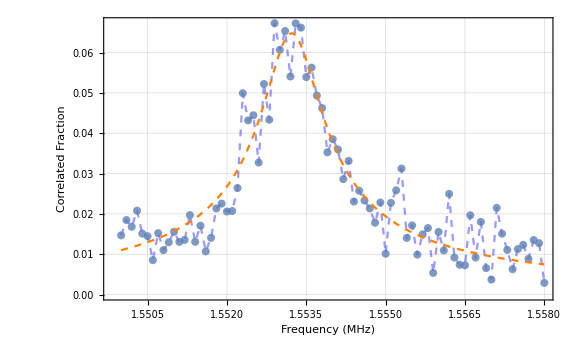
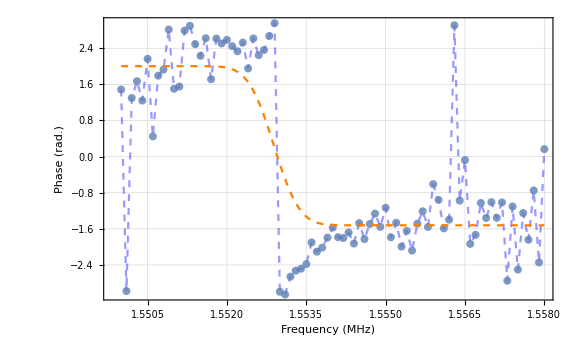

```mathematica
Join[{parameterTable},extraTables]
{
amplitudeFinalPlots[[1]],
phaseFinalPlots[[1]]
}
```

## Full

Optimal Voltage: 47.4217 V

| System
# Counts | 10000
DDS Att. (dB) | 10.
Step Size (kHz) | 0.100117
397nm Freq. (MHz) | 50.
397nm Ampl. (% Ampl.) | 105.

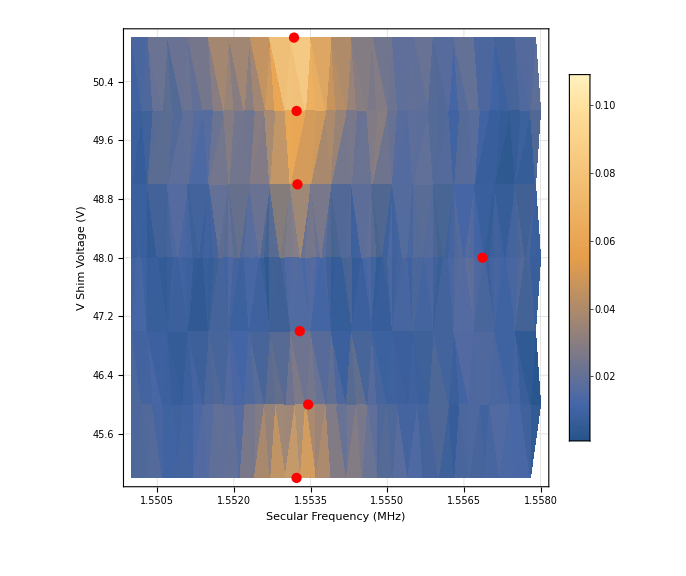
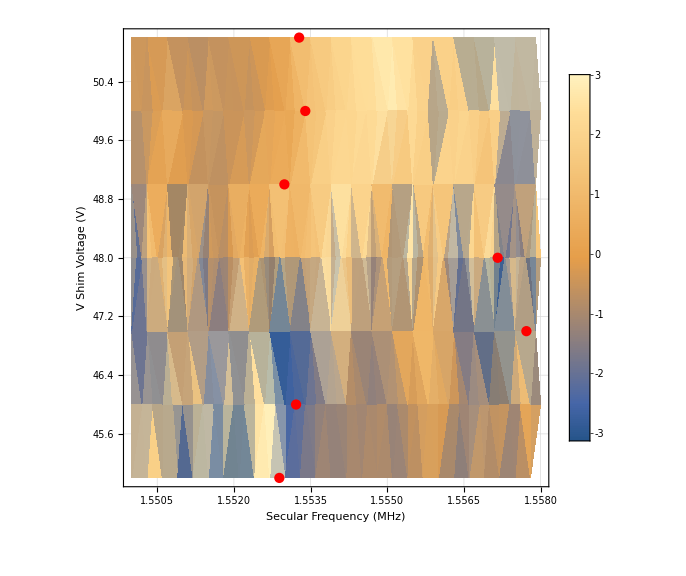
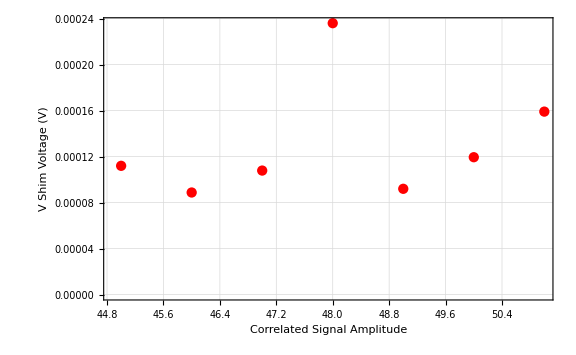

```mathematica
Print["Optimal Voltage: "<>ToString[Median[Values[minVoltageArr]]]<>" V"];
parameterTable
{
Show[amplitudeDensityPlot,amplitudeResPlot],
Show[phaseDensityPlot,phaseResPlot],
minimumAmplitudePlot
}
```

## Deprecated

## Importing

```mathematica
(*(*get parameters*)
xArr=Import[#,{"/datasets/xArr"}]*1*^6&/@filenamesDJ;
xArr=Sort/@xArr;*)
```

## Processing

```mathematica
(*get time difference in seconds*)
(*datasets=(#[[;;,3]]-#[[;;,2]])/(1*^9)&/@datafile;*)
```

```mathematica
(*get total count times*)
(*datasetTimes=N[(#[[-1,3]]-#[[1,2]])/(1*^9)]&/@datafile;*)
(*get total count rates*)
(*datasetRates=numPoints/datasetTimes;*)
```

## Fitting

### Preprocess

```mathematica
(*fitData=histData;*)
```

```mathematica
(*(*remove offset*)
(*fitData=#-Mean[#]&/@fitData[[;;,;;,2]];*)*)
```

```mathematica
(*(*fit constraints*)
fitConstraints={
0<=a<=40,
1*2*π<=b<=2*π*3,
0<=c<=2π
};*)
```

```mathematica
(*RealignPhase[data_]:=Module[
{
normalValues=Clip[data[[;;,2]],{-π/2,π},{0,0}],
realignedValues=Clip[2π+Clip[data[[;;,2]],{-π,-π/2},{0,0}],{π,(3π)/2},{0,0}]
},
Return[Transpose[{data[[;;,1]],normalValues+realignedValues}]];
];*)
```

### Fitting

```mathematica
(*(*fit sine*)
AbsoluteTiming[dataFits=ParallelMap[
NonlinearModelFit[#,
Join[{a*Sin[b*x+c]+d},fitConstraints],
{a,b,c,d},x,
Method->Automatic,
MaxIterations->1000
]&,
histData
];]*)
```

```mathematica
(*(*extract parameters*)
fittedParameterTables=#["ParameterTable"][[1]]&/@dataFits;
fittedParameters=fittedParameterTables[[;;,1,2;;5,{2,3}]];
{fittedAmplitudes,fittedFrequencies,fittedPhases,fittedOffsets}=Transpose[fittedParameters];*)
```

```mathematica
(*(*create step model*)
stepModel=α*HeavisideTheta[x-β]+γ;
stepConstraints={Abs[α]<=1.5*π,(*β>0,*)Abs[γ]<1.5*π};
(*fit phase & get fit functions*)
AbsoluteTiming[
stepFits=ParallelMap[
FindFit[#,Join[{stepModel,stepConstraints}],{α,β,γ},x,MaxIterations->1000]&,
rawPhaseData
];
]*)
```

### Plot Fit

```mathematica
(*fitSinFunc[A_,ω_,ϕ_,C_]:=A*Sin[ω*x+ϕ]+C;*)
```

```mathematica
(*(*create plot of fitted equation*)
fitSinEqns=fitSinFunc@@#&/@fittedParameters[[;;,;;,1]];
fitSinPlots=Plot[#,{x,histData[[1,1,1]],histData[[1,-1,1]]}]&/@fitSinEqns;*)
```

```mathematica
(*(*combine figures*)
combinedPlots=MapThread[Show[#1,#2]&,{histPlots,fitSinPlots}];*)
```

### Phase

```mathematica
(*PhaseThreshold[dataset_]:=Module[
{
phaseValues=dataset[[;;,2]],
phaseThreshold
},
phaseThreshold=FindThreshold[Arg[Exp[ⅈ*phaseValues]]];
Return[phaseThreshold]
];*)
```

```mathematica
(*PhaseThresholdRDX[dataset_]:=Module[
{
phaseValues=dataset[[;;,2]],
phaseThreshold1,
phaseValues2,
phaseThreshold2,
phaseThreshold3,
th2,th3
},
phaseThreshold1=FindThreshold[Arg[Exp[ⅈ*phaseValues]]];
phaseValues2=Arg[Exp[ⅈ*(phaseValues-phaseThreshold1)]];
phaseThreshold2=FindThreshold[phaseValues2];
th2=GroupBy[phaseValues2,#>phaseThreshold2&,Mean];
th3=Mean[Values[th2]];
phaseThreshold3=Total[Abs[Values[th2]]];
Return[phaseThreshold1+th3]
];*)
```

```mathematica
(*PhaseThresholdRDX[dataset_]:=Module[
{
phaseValues=dataset[[;;,2]],
phaseThreshold1,
phaseValues2,
phaseThreshold2,
phaseThreshold3,
th2,th3
},
phaseThreshold1=FindThreshold[Arg[Exp[ⅈ*phaseValues]]];
(*phaseValues2=Arg[Exp[ⅈ*(phaseValues-phaseThreshold1)]];*)
(*phaseThreshold2=FindThreshold[phaseValues2];*)
th2=GroupBy[phaseValues,#>phaseThreshold1&,Mean];
th3=Mean[Values[th2]];
(*phaseThreshold3=Total[Abs[Values[th2]]];*)
Return[th3]
];*)
```

## Analysis

### Linear Complex Fit

```mathematica
(*kk0=GroupBy[dataset,#[[1]]&,Transpose[{#[[;;,2]],#[[;;,3]]*Exp[ⅈ*#[[;;,4]]]}]&]//KeySort;
kk0=kk0[[1]];
kkComplex={Re[#],Im[#]}&/@kk0[[;;,2]];*)
```

```mathematica
(*linModel0=LinearModelFit[kkComplex,x,x];
linModel0Params=linModel0["BestFitParameters"];
kkComplexHues={Hue[#]}&/@((kk0[[;;,1]]-Min[kk0[[;;,1]]])/(2*(Max[kk0[[;;,1]]]-Min[kk0[[;;,1]]])));
{
ListPlot[Abs/@kk0],
Show[
{
ListPlot[
Transpose[{kkComplex}],
PlotStyle->kkComplexHues
],
Plot[
linModel0[x],
{x,Min[kkComplex[[;;,1]]],Max[kkComplex[[;;,1]]]},
PlotStyle->{Dashed,Orange}
]
}
],
MatrixForm[linModel0["BestFitParameters"]]
}*)
```

### Fit Parameterized Data

```mathematica
(*kkProjection=kk0[[;;,1]].Normalize[{1,linModel0Params[[2]]}];
kkParameterized=Transpose[{kk0[[;;,1]],kkProjection}];
linModel1=LinearModelFit[kkParameterized,x,x];
{
linModel1Plot=Show[
{
ListPlot[
{kkParameterized,kkParameterized},
Joined->{False,True},
PlotStyle->{{Automatic},{Dashed,Blue,Opacity[0.3]}}
],
Plot[
linModel1[x],
{x,Min[kk0[[;;,1]]],Max[kk0[[;;,1]]]},
PlotStyle->{Dashed,Orange}
]
}
],
linModel1Params=linModel1["BestFitParameters"]
}*)
```

### Calculate Optimal Voltage

```mathematica
(*-1/linModel1Params[[2]]((linModel0Params[[2]]*linModel0Params[[1]])/(1+linModel0Params[[2]]^2)+linModel1Params[[1]])*)
```

## Plotting

```mathematica
(*yz1=HistogramList[#,1000]&/@datasets;
mzdp1=Sqrt[GetSingleSidedY[Abs[Fourier[yz1[[1,2]]]]^2]];
ListLinePlot[%]*)
```